## MATH2200: Applied Mathematics — Exam 2010

## Instructions

Time allowed : 2 hours

ENTER YOUR STUDENT NUMBER IN THE BOX ABOVE

Save your notebook now and save regularly during the test. Save either on the network server in the MCL or to a memory stick, in case your computer crashes.

This is an “open-book” exam. You are permitted to bring in printed or electronic copies of your lecture notes and assignment solutions, and to access electronic resources such as the Documentation Center and the internet.

Spoken or electronic communication via email, messaging, chat, file transfer, etc. is not permitted. Such action may result in your being deprived of any credit for this examination or even, in some cases, for the whole unit. This will apply regardless of whether the material has been used at the time it is found.

Insert your solutions—both Mathematica code and text—directly into the Notebook below the Solution cell that immediately follows the part of the question that you are answering.

When asked to do so by the examination supervisor, upload your solutions using the Upload button above. Stay seated and do not talk until the examination supervisors verify that all notebooks have been uploaded.

## Mathematica Calculations and Programming [20 Marks]

Orthonormal polynomials [7 Marks]

Construct a set of linearly independent polynomials, u_n(x), 0≤n≤4, such that u'_n(±1)==0. Hint: the constant function u_0(x)=1 satisfies u'_0(±1)==0. The polynomial (1-x^2) x^(n-1) vanishes at both ±1. [2 Marks]

Explain why polynomials of degree 1 or 2 cannot have zero derivative at both ±1. [1 Mark]

Orthogonalize the u_n(x) with respect to the inner product ⟨f,g⟩:=∫_-1^1 f gⅆx to obtain an orthonormal set polynomials over the interval [-1,1]. [2 Marks]

Plot these polynomials. How many nodes does each u_n(x) have in the interval [-1,1]?  [2 Marks]

Solution

Define u_n(x):

```mathematica
Subscript[u, 0](x_)=1;
```

```mathematica
Subscript[u, n_](x_)=∫(1-x^2) x^(n-1)ⅆx
```

-x^n (x^2/(n+2)-1/n)

Verify that this set of polynomials satisfy u'_n(±1)==0:

```mathematica
{Subscript[u, 0]'(-1),Subscript[u, 0]'(1),Subscript[u, n]'(-1),Subscript[u, n]'(1)}//Simplify
```

{0,0,0,0}

The degree 1 polynomial a x+b has constant derivative a, which would require a=0 leading to a constant function.

The degree 2 (quadratic) polynomial a x^2+b x+c has derivative 2a x+b, which would require 2a+b==-2a+b==0⇒a==b==0.

Construct a set of linearly independent polynomials, u_n(x), 0≤n≤4:

```mathematica
us=Table[Subscript[u, n](x),{n,0,4}]
```

{1,-x (x^2/3-1),-x^2 (x^2/4-1/2),-x^3 (x^2/5-1/3),-x^4 (x^2/6-1/4)}

Define the inner product:

```mathematica
⟨f_,g_⟩:=∫_-1^1 f gⅆx;
```

Construct the corresponding orthonormal set of polynomials over the interval [-1,1]:

```mathematica
vs=Orthogonalize[us,AngleBracket]//Factor
```

{1/(√2),-1/2 √(35/34) x (x^2-3),-1/8 √(7/6) (15 x^4-30 x^2+7),-1/16 √(77/221) x (153 x^4-290 x^2+105),-1/32 √(65/159) (693 x^6-1365 x^4+651 x^2-43)}

Add a Tooltip to identify u_n(x):

```mathematica
Tooltip@@@Transpose[{vs,Range[Length[vs]]-1}]
```

{1/(√2),-1/2 √(35/34) x (x^2-3),-1/8 √(7/6) (15 x^4-30 x^2+7),-1/16 √(77/221) x (153 x^4-290 x^2+105),-1/32 √(65/159) (693 x^6-1365 x^4+651 x^2-43)}

Plot this orthonormal set of polynomials over [-1,1]:

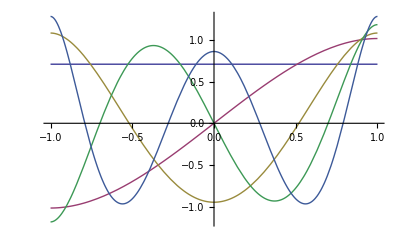

```mathematica
Plot[%,{x,-1,1}]
```

Clearly u_n(x) has n nodes in the interval [-1,1].

Nondecreasing function  [3 Marks]

Find values of real coefficients a and b such that f_(a,b)(x)=x^4+2 a x^3+b x^2+(1-3 a) x+4 is nondecreasing for -1≤x≤1. Hint: You may find using Manipulate to plot f_(a,b)(x) and f'_(a,b)(x) together over [-1,1] for various values of a and b helpful. [3 Marks]

Solution

Define f_(a,b)(x):

```mathematica
Subscript[f, a_,b_](x_)=x^4+2 a x^3+b x^2+(1-3 a) x+4;
```

Use Manipulate to plot f_(a,b)(x) and f'_(a,b)(x) together over [-1,1] for various values of a and b. One finds that a≈0 and b≈-3/2:

```mathematica
Manipulate[Plot[{Tooltip[Subscript[f, a,b](x),f],Tooltip[Subscript[f, a,b]'(x),f']},{x,-1,1},PlotRange->{-2,6}],{a,-1,1},{b,-2,2},SaveDefinitions->True]
```

Use Reduce on the requirement ∀_(x,-1≤x≤1)f'_(a,b)(x)≥0 yields the unique answer:

```mathematica
coefs=Reduce[∀_(x,-1≤x≤1)Subscript[f, a,b]'(x)≥0]
```

a==0∧b==-3/2

The derivative is clearly nonnegative for -1≤x≤1:

```mathematica
Subscript[f, a,b]'(x)/.ToRules[coefs]//Factor
```

(x+1) (2 x-1)^2

A plot gives visual confirmation that the function is nondecreasing:

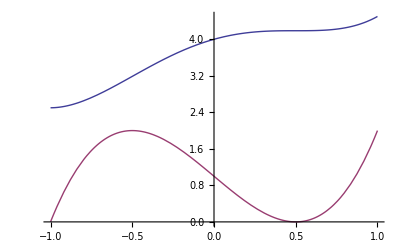

```mathematica
Plot[Evaluate[{Subscript[f, a,b](x),Subscript[f, a,b]'(x)}/.ToRules[coefs]],{x,-1,1}]
```

Nonlinear integral equation  [4 Marks]

Consider the integral equation

P(x)==∫_0^∞ ⅇ^-y P(y) P(x+y)ⅆy

Even though this integral equation is nonlinear, its polynomial solutions of degree n,

P_n(x)==∑_(k=0)^n a_(n,k)x^k, a_(n,n)≠0

can be found analytically.

Verify that P_0(x)==1. [1 Marks]

Obtain P_n(x) for n=1,2,3. [3 Marks]

Solution

Verify that P_0(x)==1.

```mathematica
Subscript[P, 0](x_)=1;
```

```mathematica
Subscript[P, 0](x)==∫_0^∞ ⅇ^-y Subscript[P, 0](y) Subscript[P, 0](x+y)ⅆy
```

True

Define P_n(x):

```mathematica
Subscript[P, n_](x_):=∑_(k=0)^n Subscript[a, n,k] x^k
```

Determine the coefficients a_(n,k) via (Maclaurin) series expansion:

```mathematica
cs[n_]:=cs[n]=Reduce[{Subscript[P, n](x)==∫_0^∞ ⅇ^-y Subscript[P, n](y) Subscript[P, n](x+y)ⅆy+O[x]^(n+1),Subscript[a, n,n]≠0}]
```

```mathematica
Table[{n,cs[n]},{n,3}]
```

(1 | a_(1,1)==-1∧a_(1,0)==2
2 | a_(2,2)==1/2∧a_(2,1)==-3∧a_(2,0)==3
3 | a_(3,3)==-1/6∧a_(3,2)==2∧a_(3,1)==-6∧a_(3,0)==4)

Obtain P_n(x) for n=1,2,3:

```mathematica
Table[{n,Subscript[P, n](x)/.First@Solve@cs[n]},{n,0,3}]
```

(0 | 1
1 | 2-x
2 | x^2/2-3 x+3
3 | -x^3/6+2 x^2-6 x+4)

It can be shown that P_n(x)==L_n^1(x):

```mathematica
Table[{n,Subscript[L, n]^1(x)//Expand},{n,0,3}]
```

(0 | 1
1 | 2-x
2 | x^2/2-3 x+3
3 | -x^3/6+2 x^2-6 x+4)

Recursion [6 Marks]

Consider the continuous function ϕ(x) defined by the recursive equation

ϕ(x)==∑_(k=0)^3 c_k ϕ(2x-k)

where ϕ(x)==0 for x≤0 and x≥3, ϕ(1)+ϕ(2)==1, and

c_0=3/5,c_1=6/5,c_2=2/5,c_3=-1/5.

The values of ϕ(1) and ϕ(2) are determined by solving a matrix equation:

(ϕ(1)
ϕ(2))==(c_1 | c_0
c_3 | c_2).(ϕ(1)
ϕ(2)).

Compute ϕ(1) and ϕ(2). [2 Marks]

Implement the recursive equation using dynamic programming. Note that ϕ(x)==0 for x≤0 and x≥3. As a check you should find that ϕ(3/2)==0. [2 Marks]

Use ListPlot (or DiscretePlot) to plot ϕ(x) over [0,3] by evaluating ϕ(x) at points x=n 2^-m where 0≤m≤7 and n≥0 are integers. [2 Marks]

Solution

Define the coefficients:

```mathematica
{Subscript[c, 0]=3/5,Subscript[c, 1]=6/5,Subscript[c, 2]=2/5,Subscript[c, 3]=-1/5};
```

Compute ϕ(1) and ϕ(2):

```mathematica
Solve[{({{Subscript[c, 1], Subscript[c, 0]}, {Subscript[c, 3], Subscript[c, 2]}}).({{ϕ(1)}, {ϕ(2)}})== ({{ϕ(1)}, {ϕ(2)}}),ϕ(1)+ϕ(2)==1}]
```

{{ϕ(1)→3/2,ϕ(2)→-1/2}}

```mathematica
{ϕ(1),ϕ(2)}={ϕ(1),ϕ(2)}/.First[%]
```

{3/2,-1/2}

Implement the recursive equation:

```mathematica
ϕ(x_/;x≤0∨x≥3):=0
```

```mathematica
ϕ(x_):=ϕ(x)=∑_(k=0)^3 Subscript[c, k] ϕ(2 x-k)
```

Check that ϕ(3/2)==0:

```mathematica
ϕ(3/2)==0
```

True

Use DiscretePlot to plot ϕ(x) over [0,3] by evaluating ϕ(x) at points x=n 2^-m where 0≤m≤7 and n≥0 are integers:

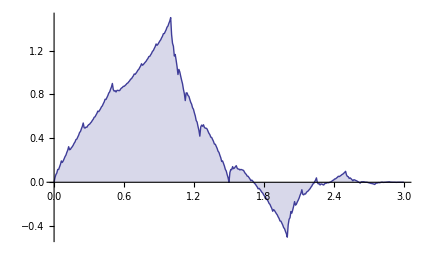

```mathematica
DiscretePlot[ϕ(x),{x,0,3,2^-7}]
```

## Centrosymmetric Matrices [20 Marks]

Amongst the many special types of matrices are centrosymmetric ones. When a centrosymmetric matrix is also symmetric it is called bi-symmetric. The SymmetricMatrixQ predicate tests whether a matrix is symmetric.

The following predicate tests if a matrix is centrosymmetric:

```mathematica
CentroSymmetricMatrixQ[M_]:=Simplify[Reverse[M]==Reverse/@M]
```

The following predicate tests if a matrix is bisymmetric:

```mathematica
BiSymmetricMatrixQ[M_]:=SymmetricMatrixQ[M]∧CentroSymmetricMatrixQ[M]
```

Here is an example of an n×n symmetric centrosymmetric matrix:

```mathematica
J[n_]:= Map[Reverse,IdentityMatrix[n]]
```

Check that J[4] is centrosymmetric:

```mathematica
J[4]
```

(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
CentroSymmetricMatrixQ[J[4]]
```

True

Code for constructing an arbitrary 4×4 centrosymmetric matrix:

```mathematica
CentroSymmetricMatrix[r1_List,r2_List]:={r1,r2,Reverse[r2],Reverse[r1]}/;Length[r1]==Length[r2]==4
```

Code for constructing an arbitrary 4×4 bisymmetric matrix:

```mathematica
BiSymmetricMatrix[r1_List,{a_,b_}]:=CentroSymmetricMatrix[r1,{r1⟦2⟧,a,b,r1⟦3⟧}]/;Length[r1]==4
```

```mathematica
BiSymmetricMatrix[{a,b,c,d},{e,f}]
```

(a | b | c | d
b | e | f | c
c | f | e | b
d | c | b | a)

```mathematica
BiSymmetricMatrixQ[%]
```

True

### Properties [10 Marks]

Properties of centrosymmetric matrices [4 Marks]

Show that the product of two 4×4 centrosymmetric matrices is centrosymmetric. [1 Mark]

Show that any 4×4 centrosymmetric matrix commutes with J[4]. [1 Mark]

Show that the transpose of any 4×4 centrosymmetric matrices is centrosymmetric. [1 Mark]

Show that the product of two 4×4 bisymmetric matrices is centrosymmetric but not necessarily symmetric. [1 Mark]

Solution

H1 and H2 are general (4×4) centrosymmetric matrices:

```mathematica
H1=CentroSymmetricMatrix[Table[Subscript[α, i],{i,4}],Table[Subscript[β, i],{i,4}]]
```

(α_1 | α_2 | α_3 | α_4
β_1 | β_2 | β_3 | β_4
β_4 | β_3 | β_2 | β_1
α_4 | α_3 | α_2 | α_1)

```mathematica
H2=CentroSymmetricMatrix[Table[Subscript[γ, i],{i,4}],Table[Subscript[δ, i],{i,4}]]
```

(γ_1 | γ_2 | γ_3 | γ_4
δ_1 | δ_2 | δ_3 | δ_4
δ_4 | δ_3 | δ_2 | δ_1
γ_4 | γ_3 | γ_2 | γ_1)

```mathematica
CentroSymmetricMatrixQ[H1]
```

True

```mathematica
CentroSymmetricMatrixQ[H2]
```

True

The sum of two 4×4 centrosymmetric matrices is centrosymmetric:

```mathematica
CentroSymmetricMatrixQ[H1+H2]
```

True

The product of two 4×4 centrosymmetric matrices is centrosymmetric:

```mathematica
CentroSymmetricMatrixQ[H1.H2]
```

True

Any 4×4 centrosymmetric matrix commutes with J[4]:

```mathematica
H1.J[4]==J[4].H1
```

True

The transpose of any 4×4 centrosymmetric matrix is centrosymmetric.

```mathematica
CentroSymmetricMatrixQ[Transpose[H1]]
```

True

The product of a 4×4 centrosymmetric matrix and a 4×4 symmetric matrix is not necessarily symmetric:

```mathematica
sym=SparseArray[{{i_,j_}->Subscript[a, Min[i,j],Max[i,j]]},{4,4}]//Normal
```

(a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4)
a_(1,2) | a_(2,2) | a_(2,3) | a_(2,4)
a_(1,3) | a_(2,3) | a_(3,3) | a_(3,4)
a_(1,4) | a_(2,4) | a_(3,4) | a_(4,4))

```mathematica
SymmetricMatrixQ[sym]
```

True

```mathematica
SymmetricMatrixQ[H1.sym]
```

False

The product of two 4×4 bisymmetric matrices is centrosymmetric but not necessarily symmetric:

```mathematica
Hs1=BiSymmetricMatrix[{a1,b1,c1,d1},{f1,g1}]
```

(a1 | b1 | c1 | d1
b1 | f1 | g1 | c1
c1 | g1 | f1 | b1
d1 | c1 | b1 | a1)

```mathematica
Hs2=BiSymmetricMatrix[{a2,b2,c2,d2},{f2,g2}]
```

(a2 | b2 | c2 | d2
b2 | f2 | g2 | c2
c2 | g2 | f2 | b2
d2 | c2 | b2 | a2)

```mathematica
Map[CentroSymmetricMatrixQ,{Hs1,Hs2}]
```

{True,True}

```mathematica
Map[SymmetricMatrixQ,{Hs1,Hs2}]
```

{True,True}

```mathematica
CentroSymmetricMatrixQ[Hs1.Hs2]
```

True

```mathematica
SymmetricMatrixQ[Hs1.Hs2]
```

False

Vector space [1 Mark]

The set of n×n centrosymmetric matrices forms a vector space.

What is the dimension of the vector space of 4×4 centrosymmetric matrices? [1 Mark]

Solution

The dimension of the vector space of 4×4 centrosymmetric matrices is 8 (8 independent elements).

Matrix exponential  [1 Mark]

The sum of n×n centrosymmetric matrices is centrosymmetric. Also, the product of n×n centrosymmetric matrices is centrosymmetric, which implies that the inverse of any invertible centrosymmetric matrix is centrosymmetric.

Let matrix A be centrosymmetric. Is the matrix exponential of A centrosymmetric? Why? [1 Mark]

Solution

Yes,  MatrixExp[t A] is centrosymmetric. The sum

∑_(k=0)^∞ t^k/(k!)A^k==ⅇ^(t A)

is centrosymmetric since A^k is the product of k centrosymmetric matrices and the sum of centrosymmetric matrices is also centrosymmetric.

Even and odd vectors [1 Mark]

Define an n-vector v as even if J[n].v==v, and odd if J[n].v==-v.

Write a function which returns 1 if a vector is even, -1 if it is odd, and 0 otherwise. [1 Mark]

Solution

The action of J[n] on a vector is to reverse the vector. Here is a test function which returns 1 if a vector is even and 1 if it is odd and -1 otherwise:

```mathematica
EvenOddVectorTest[v_List]:=Switch[Reverse[v],v,1,-v,-1,_,0]
```

Check that it works:

```mathematica
EvenOddVectorTest[{a,b,b,a}]
```

1

```mathematica
EvenOddVectorTest[{a,b,-b,-a}]
```

-1

```mathematica
EvenOddVectorTest[{a,b,c,d}]
```

0

Eigenspaces [1 Mark]

Commuting matrices share eigenvectors. The eigenvectors of any n×n centrosymmetric matrix are contained in the eigenspaces of J[n].

What are the eigenspaces of J[4]? [1 Mark]

Solution

Compute the eigenspaces of J[4]:

```mathematica
Eigensystem[J[4]]
```

(-1 | -1 | 1 | 1
{-1,0,0,1} | {0,-1,1,0} | {1,0,0,1} | {0,1,1,0})

Remark: The eigenvectors corresponding to eigenvalue -1 are odd, while those corresponding to 1 are even.

Skew-symmetric matrices [2 Marks]

Give an example of a skew-symmetric 4×4 matrix A which is also centrosymmetric. Is MatrixExp[t A] orthogonal? [2 Marks]

Solution

The following predicate tests if a matrix is skew-symmetric:

```mathematica
SkewSymmetricMatrixQ[A_]:=Transpose[A]==-A
```

The following predicate tests if a matrix is orthogonal:

```mathematica
OrthogonalMatrixQ[A_]:=Simplify[A.Transpose[A]==IdentityMatrix[Length[A]]]
```

Consider the following matrix:

```mathematica
A=({{0, -1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, -1, 0}});
```

Check that A is skew-symmetric and also centrosymmetric:

```mathematica
SkewSymmetricMatrixQ[A]
```

True

```mathematica
CentroSymmetricMatrixQ[A]
```

True

Check whether MatrixExp[t A] is orthogonal:

```mathematica
MatrixExp[t A]
```

(cos(t) | -sin(t) | 0 | 0
sin(t) | cos(t) | 0 | 0
0 | 0 | cos(t) | sin(t)
0 | 0 | -sin(t) | cos(t))

```mathematica
OrthogonalMatrixQ[%]
```

True

### Tridiagonal bisymmetric matrices [3 Marks]

A symmetric tridiagonal Toeplitz matrix [3 Marks]

Consider, as we did in lectures, n equal masses, equally spaced along a stretched string which is fixed at its ends. The normal modes of oscillation of such a system correspond to the eigenvectors of the matrix T[n] where:

```mathematica
T[n_]:=ToeplitzMatrix[Join[{2,-1},ConstantArray[0,n-2]]]
```

```mathematica
Normal[T[4]]
```

(2 | -1 | 0 | 0
-1 | 2 | -1 | 0
0 | -1 | 2 | -1
0 | 0 | -1 | 2)

T[n] commutes with J[n], so the normal modes (eigenvectors) for T[n] are either even or odd.

Verify that T[4] is centrosymmetric. [1 Mark]

Use your test function to determine which eigenvectors of T[4] are even and which are odd. [1 Mark]

Ordering these eigenvectors in the order of the increasing eigenvalues, verify that they are alternately odd and even. [1 Mark]

Solution

Verify that T[4] is centrosymmetric.

```mathematica
CentroSymmetricMatrixQ[T[4]]
```

True

Compute the eigensystem of T[4] and sort in order of increasing eigenvalue:

```mathematica
{Λ,𝒰}=Reverse/@Eigensystem[T[4]]
```

(1/2 (3-√5) | 1/2 (5-√5) | 1/2 (3+√5) | 1/2 (5+√5)
{1,2+1/2 (-3+√5),2+1/2 (-3+√5),1} | {-1,-2+1/2 (5-√5),2+1/2 (-5+√5),1} | {1,2+1/2 (-3-√5),2+1/2 (-3-√5),1} | {-1,-2+1/2 (5+√5),2+1/2 (-5-√5),1})

Verify that the eigenvectors are alternately odd and even:

```mathematica
EvenOddVectorTest/@𝒰
```

{1,-1,1,-1}

Plot the eigenvectors:

```mathematica
Manipulate[ListPlot[Join[{0},𝒰⟦n⟧,{0}],Joined->True,PlotRange->{-2,2},PlotLabel->Λ⟦n⟧,DataRange->{0,Length[𝒰]+1}],{n,Range[Length[𝒰]]},SaveDefinitions->True]
```

Remark: The alternate even/odd character of the eigenvectors we saw in the preceding section illustrates a general result. The result may not be original to the paper cited below, but we mention this paper because one of its authors, Tony Cantoni is on the staff at UWA:

Linear Algebra and its Applications, 13(3), 1976, Pages 275 - 288

“Eigenvalues and eigenvectors of symmetric centrosymmetric matrices”
A.Cantoni and P.Butler

Abstract: It is proved that the eigenvectors of a symmetric centrosymmetric matrix of order N are either symmetric or skew symmetric, and that there are Ceiling[N/2] symmetric and Floor[N/2] skew-symmetric eigenvectors. Special cases are considered, in particular tridiagonal centrosymmetric matrices of both odd and even order, for which it is shown that the eigenvectors corresponding to the eigenvalues arranged in descending order are alternately symmetric (i.e. even)  and skew-symmetric (i.e. odd) provided the eigenvalues are distinct.

### Oscillations of triatomic molecules [3 Marks]

This question concerns the matrix A of 2010 Assignment 6, and a centrosymmetric tridiagonal matrix similar to it. The physics of the problem requires that k>0, K>0 and 0<β<π.

```mathematica
S[β_]=({{1/2 K (Cos[β]+1), 1/2 K Sin[β]}, {1/2 K Sin[β], 1/2 (2 k+K-K Cos[β])}});
```

```mathematica
coupling= DiagonalMatrix[{0,-k}]
```

(0 | 0
0 | -k)

```mathematica
A=ArrayFlatten[({{S[β], coupling}, {coupling, S[-β]}})]
```

(1/2 K (cos(β)+1) | 1/2 K sin(β) | 0 | 0
1/2 K sin(β) | 1/2 (2 k+K-K cos(β)) | 0 | -k
0 | 0 | 1/2 K (cos(β)+1) | -1/2 K sin(β)
0 | -k | -1/2 K sin(β) | 1/2 (2 k+K-K cos(β)))

Verify that A is symmetric:

```mathematica
SymmetricMatrixQ[A]
```

True

It is, however, neither centrosymmetric (nor tridiagonal):

```mathematica
Simplify[CentroSymmetricMatrixQ[A],{K>0,k>0,0<β<π}]
```

False

The permution matrix P34 permutes the 3rd and 4th rows (or columns):

```mathematica
P34=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}});
```

The diagonal matrix D34 flips the signs of the 3rd row (or column):

```mathematica
D34=DiagonalMatrix[{1,1,-1,1}]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)

Using P34 and D34 we can construct from A a bisymmetric tridiagonal matrix B:

```mathematica
B=Simplify[D34.P34.A.P34.D34]
```

(1/2 K (cos(β)+1) | 1/2 K sin(β) | 0 | 0
1/2 K sin(β) | 1/2 (2 k+K-K cos(β)) | k | 0
0 | k | 1/2 (2 k+K-K cos(β)) | 1/2 K sin(β)
0 | 0 | 1/2 K sin(β) | 1/2 K (cos(β)+1))

```mathematica
BiSymmetricMatrixQ[B]
```

True

Eigenvectors of B [3 Marks]

Show that the odd eigenvectors of B correspond to eigenvalues 0 and K respectively. [1 Mark]

Show that there is an even eigenvector of B corresponding to an eigenvalue strictly between 0 and K. [1 Mark]

Show that the other even eigenvector of B corresponds to an eigenvalue strictly greater than K. [1 Mark]

Solution

Compute the CharacteristicPolynomial of B (or of A):

```mathematica
char=FullSimplify[CharacteristicPolynomial[B,λ]]
```

λ (λ-K) (k K cos(β)-λ (2 k+K)+k K+λ^2)

Two of the eigenvalues are 0 and K. Consider the quadratic factor:

```mathematica
quadratic=char/(λ (λ-K))
```

k K cos(β)-λ (2 k+K)+k K+λ^2

Compute the discriminant of the quadratic:

```mathematica
Δ=Discriminant[quadratic,λ]
```

4 k^2-4 k K cos(β)+K^2

Since Δ≥0 the quadratic has 2 real roots:

```mathematica
FullSimplify[Δ≥0,{K>0,k>0,0<β<π}]
```

True

Compute and simplify the eigensystem of B in terms of the (square root) of the Discriminant of the quadratic:

```mathematica
{Λ,u}=Simplify[Eigensystem[B]]/.√Δ->δ
```

(0 | K | 1/2 (2 k+K-δ) | 1/2 (2 k+K+δ)
{-1,cot(β/2),-cot(β/2),1} | {-1,-tan(β/2),tan(β/2),1} | {1,-((-2 k+δ+K cos(β)) csc(β))/K,-((-2 k+δ+K cos(β)) csc(β))/K,1} | {1,((2 k+δ-K cos(β)) csc(β))/K,((2 k+δ-K cos(β)) csc(β))/K,1})

The odd eigenvectors of B correspond to eigenvalues 0 and K. The even eigenvectors of B correspond to eigenvalues 1/2 (2 k+K-δ) and 1/2 (2 k+K+δ) respectively.

```mathematica
EvenOddVectorTest/@u
```

{-1,-1,1,1}

The root 1/2 (2 k+K-δ) lies between 0 (where the quadratic is positive) and K (where the quadratic is negative) since 1>cos(β)>-1 for 0<β<π:

```mathematica
Factor[quadratic/.λ->0]
```

k K (cos(β)+1)

```mathematica
Factor[quadratic/.λ->K]
```

k K (cos(β)-1)

```mathematica
Simplify[0<1/2 (2 k+K-√Δ)<K,{K>0,k>0,-1<Cos[β]<1}]
```

True

The root 1/2 (2 k+K+δ) is greater than K:

```mathematica
Simplify[1/2 (2 k+K+√Δ)>K,{K>0,k>0,-1<Cos[β]<1}]
```

True

### Subalgebras of the algebra of centrosymmetric matrices [4 Marks]

A set ℳ of n×n matrices is called an algebra if:

it is a vector space under matrix addition and

it is closed under matrix multiplication, contains the n×n identity matrix, and, for any invertible matrix in ℳ, its inverse is in ℳ.

Two examples: the set of n×n centrosymmetric matrices forms an algebra; the set of n×n diagonal matrices forms an algebra.

The set of 4×4 diagonal matrices which are also centrosymmetric is an algebra, and its dimension (as a vector space) is 2.

Vector space [1 Mark]

The set of 4×4 bisymmetric matrices forms a vector space under matrix addition. What is the dimension of this vector space? Show that the set of 4×4 bisymmetric matrices is not closed under matrix multiplication. [1 Mark]

Solution

The dimension is 6 since there are 6 independent elements in a 4 by 4 bisymmetric matrix:

```mathematica
bs=BiSymmetricMatrix[{a,b,c,d},{e,f}]
```

(a | b | c | d
b | e | f | c
c | f | e | b
d | c | b | a)

```mathematica
BiSymmetricMatrixQ[bs]
```

True

The set of 4×4 bisymmetric matrices is not closed under matrix multiplication:

```mathematica
prod=bs.BiSymmetricMatrix[{a2,b2,c2,d2},{e2,f2}]
```

(a a2+b b2+c c2+d d2 | a b2+c2 d+b e2+c f2 | a c2+b2 d+c e2+b f2 | b2 c+b c2+a2 d+a d2
a2 b+c d2+b2 e+c2 f | b b2+c c2+e e2+f f2 | b2 c+b c2+e2 f+e f2 | a2 c+b d2+c2 e+b2 f
a2 c+b d2+c2 e+b2 f | b2 c+b c2+e2 f+e f2 | b b2+c c2+e e2+f f2 | a2 b+c d2+b2 e+c2 f
b2 c+b c2+a2 d+a d2 | a c2+b2 d+c e2+b f2 | a b2+c2 d+b e2+c f2 | a a2+b b2+c c2+d d2)

```mathematica
BiSymmetricMatrixQ[prod]
```

False

Pretty well any set of numbers just guessed will provide an example of matrix multiplication failing to produce a symmetric matrix:

```mathematica
prod=BiSymmetricMatrix[{1,2,3,4},{5,6}].BiSymmetricMatrix[{6,5,4,3},{2,1}]
```

(40 | 28 | 32 | 50
70 | 38 | 40 | 74
74 | 40 | 38 | 70
50 | 32 | 28 | 40)

```mathematica
SymmetricMatrixQ[prod]
```

False

Remark: As far as applications to differential equations are concerned, if we have an algebra of matrices, then the MatrixExp of any matrix in the algebra will also be in the algebra.

Algebra of dimension 4 [3 Marks]

Find a subset of the set of 4×4 bisymmetric matrices which is an algebra with a dimension (as a vector space) of at least 4. [3 Marks]

Solution

Here is an algebra with a dimension 4. It is easy to check other algebras.

Consider the following matrix:

```mathematica
Xshape[a_,b_,c_,d_]:=({{a, 0, 0, d}, {0, b, c, 0}, {0, c, b, 0}, {d, 0, 0, a}});
```

Its vector space contains the n×n identity matrix:

```mathematica
Xshape[1,1,0,0]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

It is bisymmetric:

```mathematica
M1=Xshape[a,b,c,d]
```

(a | 0 | 0 | d
0 | b | c | 0
0 | c | b | 0
d | 0 | 0 | a)

```mathematica
BiSymmetricMatrixQ[M1]
```

True

It is closed under matrix multiplication:

```mathematica
M2=Xshape[a2,b2,c2,d2]
```

(a2 | 0 | 0 | d2
0 | b2 | c2 | 0
0 | c2 | b2 | 0
d2 | 0 | 0 | a2)

```mathematica
prod=M1.M2
```

(a a2+d d2 | 0 | 0 | a2 d+a d2
0 | b b2+c c2 | b2 c+b c2 | 0
0 | b2 c+b c2 | b b2+c c2 | 0
a2 d+a d2 | 0 | 0 | a a2+d d2)

```mathematica
BiSymmetricMatrixQ[prod]
```

True

Symmetry implies commutativity:

```mathematica
M1.M2-M2.M1
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)